```mathematica
ClearAll["Global`*"]
NotebookSave[]
```

```mathematica
Tots=Transpose[{{0.00010057165907651912,0.0003406022845931523,0.0006402014479870027},{0.0009485891871399139,0.0012961743950209912,0.0015091831931895818},{0.002398503207618759,0.0023415949997066293,0.002150553074951949},{0.004585114688724832,0.003176493818349276,0.0025379973307651108},{6.888858127925316*^-6,0.000043511720581357384,0.00011146576408482298},{0.0004024518328196102,0.0007629722335856069,0.001122426292300306},{0.0015687811170360336,0.0016833384772208,0.00202279346287341},{0.0034853287399308503,0.0026319568358304482,0.00248540005184368}}]
```

{{0.000100572,0.000948589,0.0023985,0.00458511,6.88886×10^-6,0.000402452,0.00156878,0.00348533},{0.000340602,0.00129617,0.00234159,0.00317649,0.0000435117,0.000762972,0.00168334,0.00263196},{0.000640201,0.00150918,0.00215055,0.002538,0.000111466,0.00112243,0.00202279,0.0024854}}

```mathematica
time={{0.25,0.5,0.75,1.,0.125,0.375,0.625,0.875}};
```

```mathematica
tmp=TemporalData[Tots,time];
```

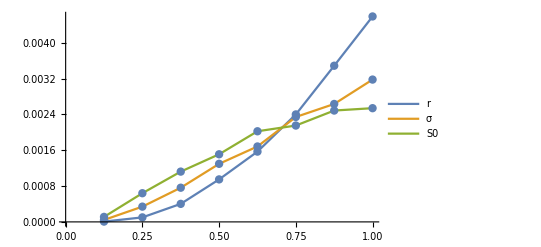

```mathematica
ListPlot[tmp,PlotLegends->{"r","σ","S0"},Joined->True,Mesh->All]
```

```mathematica
Vars=Transpose[{{0.00009111790302489225,0.00028003776005258534,0.000692573548432537},{0.0005231448921959867,0.0015428161724180445,0.002867963486243189},{0.001987249189636324,0.0033591847909178133,0.004403610823836773},{0.0022458332820427464,0.0036861312258917676,0.002725724722454316},{7.393768280637135*10^(-6),0.00004322870002285361,0.0001161124225516977},{0.00003199162784756208,0.0008141625428859635,0.0014995170259100754},{0.002318111764559229,0.0023317514514321893,0.0025555873735175977},{0.002609076750504108,0.0011721571568611298,0.004146709682594971}}];
```

```mathematica
time={{0.25,0.5,0.75,1.,0.125,0.375,0.625,0.875}};
```

```mathematica
tmp2=TemporalData[Vars,time];
```

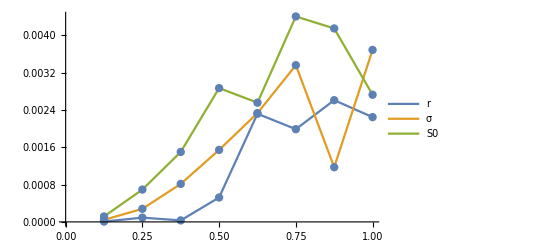

```mathematica
ListPlot[tmp2,PlotLegends->{"r","σ","S0"},Joined->True,Mesh->All]
```

```mathematica
NotebookSave[]
```